```mathematica
<<VectorAnalysis`
```

```mathematica
<<VectorFieldPlots`
```

General::obspkg: "VectorFieldPlots`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
SetCoordinates[Spherical[r,θ,ϕ]]
```

Spherical[r,θ,ϕ]

```mathematica
Table[√(Cos[θ]/(i-1)),{i,0,0.8,0.2}]
```

{√(-1. Cos[θ]),1.11803 √(-Cos[θ]),1.29099 √(-Cos[θ]),1.58114 √(-Cos[θ]),2.23607 √(-Cos[θ])}

```mathematica
Table[-√(Cos[θ]/(i-1)),{i,0,0.8,0.2}]
```

{-√(-1. Cos[θ]),-1.11803 √(-Cos[θ]),-1.29099 √(-Cos[θ]),-1.58114 √(-Cos[θ]),-2.23607 √(-Cos[θ])}

```mathematica
Table[i*Sin[θ]^2,{i,1,2.58,0.5}]
```

{1. Sin[θ]^2,1.5 Sin[θ]^2,2. Sin[θ]^2,2.5 Sin[θ]^2}

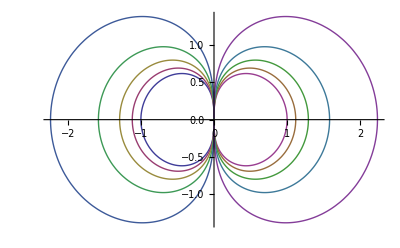

```mathematica
g1=PolarPlot[{√(-1. Cos[θ]),1.118033988749895 √(-Cos[θ]),1.2909944487358056 √(-Cos[θ]),1.5811388300841898 √(-Cos[θ]),2.23606797749979 √(-Cos[θ]),-√(-1. Cos[θ]),-1.118033988749895 √(-Cos[θ]),-1.2909944487358056 √(-Cos[θ]),-1.5811388300841898 √(-Cos[θ]),-2.23606797749979 √(-Cos[θ])},{θ,0,2π}]
```

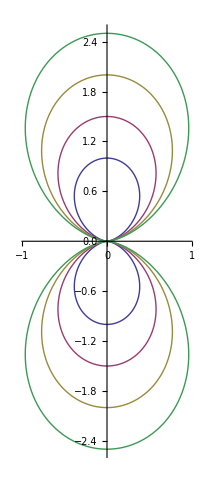

```mathematica
g2=PolarPlot[{1. Sin[θ]^2,1.5 Sin[θ]^2,2. Sin[θ]^2,2.5 Sin[θ]^2},{θ,0,2π}]
```

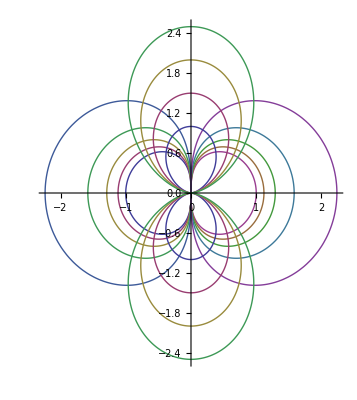

```mathematica
Show[{g1,g2}]
```